```mathematica
ClearAll["Global`*"]
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out", "schaeferTurek"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/schaeferTurek

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
getSizes[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,4] &/@StringCases[thelist, RegularExpression["size([0-9]*)"]]] 
sizes = getSizes[srts];
permutations = Ordering[sizes];
sizes = sizes[[permutations]];
cumulants = cumulants[[permutations]];
srts = srts[[permutations]];
```

```mathematica
dragData[input_] := Drop[Map[Delete[#,3]&,input],00];
liftData[input_] := Drop[Map[Delete[#,2]&,input],00];
valuesOnly[data_]:=Flatten[Map[Delete[#,1]&,data]];
myImport[list_] := Drop[#,1]&/@Import /@ list;
dataFrequency[list_] := Abs[Fourier[ #[[2]]&/@list]];

maximaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],-2];
minimaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],2]

lastWavelimits[data_]:=Flatten[ Take[maximaPositions[data],-2]];
lastWavelength[data_]:=Differences[lastWavelimits[data]][[1]];

lastWave[data_]  := Take[data,lastWavelimits[data]];
dragResult = 5.8190;
liftResult = 0.0110;
means[datas_] := Map[Mean[valuesOnly[#]]&,datas];
bothLiftMeansPlotReady := {Transpose[{sizes,means[lastWave /@liftData /@myImport[cumulants]]-liftResult}],Transpose[{sizes,means[lastWave/@liftData /@ myImport[srts]]-liftResult}]};
bothDragMeansPlotReady := {Transpose[{sizes,means[lastWave /@dragData /@myImport[cumulants]]-dragResult}],Transpose[{sizes,means[lastWave/@dragData /@ myImport[srts]]-dragResult }]};
```

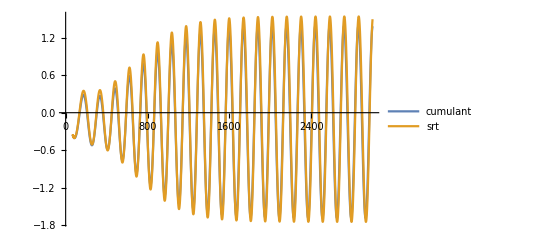

```mathematica
nr=6;
ListLinePlot[{(liftData/@myImport[cumulants])[[nr]],(liftData/@myImport[srts])[[nr]]} , PlotLegends->{"cumulant","srt"}]
```

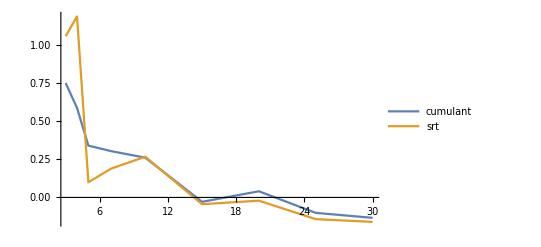

```mathematica
ListLinePlot[bothDragMeansPlotReady, PlotLegends->{"cumulant","srt"}, PlotRange->All]
```

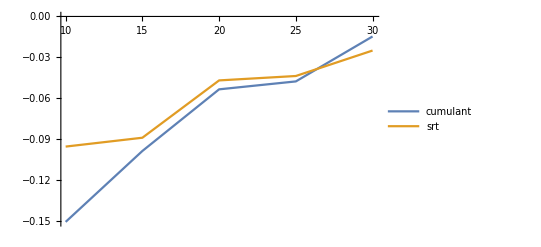

```mathematica
ListLinePlot[Drop[#,4]&/@bothLiftMeansPlotReady, PlotLegends->{"cumulant","srt"}]
```